# RISPs from graphs

This notebook uses the Nevanlinna representation (see ) to generate rational inner skew products from adjacency matrices of simple undirected graphs - as such matrices are symmetric, they provide a natural source of such functions.

```mathematica
(* Cayley transforms*)
disk2plane[z_]:= I (1 - z)/(1+z);
plane2disk[z_] := (1 + z I)/(1 - z I);
```

```mathematica
(* functions for computing the location and multipliers of rotation bands *)
```

```mathematica
fixedFinder[f_, omega_]:= Module[{temp,fixedpoint},
temp=ReplaceAll[z,Solve[f[z, w]==z, z]]/.w->omega;
Select[temp, Abs[#]<1&, 1]]
rotNumberBand[f_, omega_]:= Module[{fp},
fp = fixedFinder[f, omega];
Arg[D[f[z, omega], z]/.z->fp]
]
```

```mathematica
n=6; (* choose the number of vertices and load the graph database. We convert this to an array of matrices *)
AMatrices=AdjacencyMatrix/@(GraphData/@GraphData[n])//Normal;
```

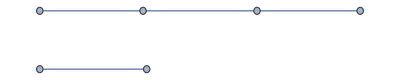

```mathematica
(* Pick a random adjacency matrix *)
A = RandomChoice[AMatrices];
AdjacencyGraph[A]
```

```mathematica
(* build the pieces of the Nevanlinna representation *)
Y2 = {{0}};
Y1 =IdentityMatrix[n-1];
Y = ArrayFlatten@ReleaseHold@DiagonalMatrix[Hold /@ {Y1, Y2}];
alpha = {1,0,0,0,0,0};
zY = z Y + (IdentityMatrix[n]-Y)w;
```

```mathematica
(* translate to a rational inner Schur function via composition with Cayley transforms *)
```

```mathematica
f[w_,z_]=Simplify[plane2disk[((Inverse[A - zY].alpha).alpha/.{w->disk2plane[w], z->disk2plane[z]})]];

(* compute level curves to identify singularities (SF-points) *)
Clear[g1];
{g1[w_, c_]}= (z/.Solve[f[z,w]==  c,z]);
levelcurves =Show[ParametricPlot[{{Arg[g1[Exp[I t], Exp[I #]]], t},{Arg[g2[Exp[I t], Exp[I #]]], t}}, {t, -Pi,Pi}, PlotStyle->Hue[#/(2Pi)], PlotRange->All]&/@Range[-Pi, Pi]];
```

```mathematica
(* Compute fixed point curves *)
```

```mathematica
Clear[curve];
curve[z_]= w/.Solve[f[z,w]==  z,w];
fixed=ListPlot[Table[Inner[List,Flatten[ConstantArray[t, {1,Length[curve[z]]}]],Arg[curve[Exp[I t]]], List], {t, Range[-Pi, Pi, .005]}], PlotStyle->{{Black}}, AspectRatio->Full, PlotRange->All];
```

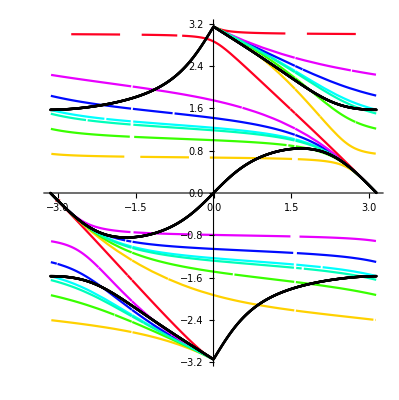

```mathematica
(* Plot fixed point curves and level curves *)
Show[levelcurves, fixed]
```

```mathematica
(* you can check a singularity directly - remember that these are Arg plots, so convert back to complex numbers *)
f[1,-1]
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Indeterminate

```mathematica
(* You can compute the value by choosing a nearby point *)f[-.99I,-.99I]
```

0.960608-1.09303×10^-18 ⅈ

```mathematica
"convert to exponential"-3/5+(4 ⅈ)/5With[{n=Abs[-3/5+(4 ⅈ)/5],a=Arg[-3/5+(4 ⅈ)/5]},Defer[n ⅇ^(ⅈ a)]]
```

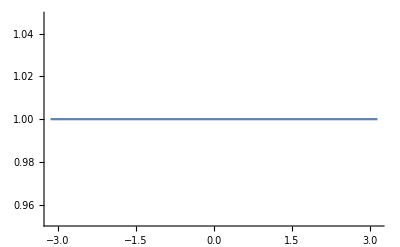

```mathematica
(* test a strip to verify that the function is inner *)Plot[Abs[f[1, Exp[I t]]], {t, -Pi, Pi}]
```

```mathematica
(* compute contact order from the power series expansion at a singularity *)Series[g1[z, t], {z,-1, 5}]//Simplify
```

1+2 (z+1)+((7-5 t) (z+1)^2)/(2-2 t)+((6-8 t+3 t^2) (z+1)^3)/(-1+t)^2+((-81+155 t-111 t^2+29 t^3) (z+1)^4)/(8 (-1+t)^3)+((271-672 t+698 t^2-352 t^3+71 t^4) (z+1)^5)/(16 (-1+t)^4)+O[z+1]^6

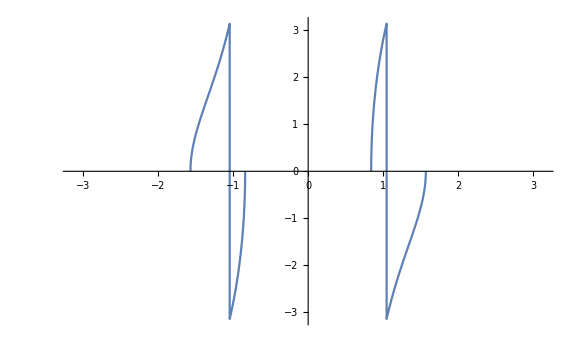

```mathematica
(* compute rotation bands *)
Plot[rotNumberBand[f, Exp[I s]], {s, -Pi, Pi}, ImageSize->Large, PlotPoints->500,PlotRange->{{-Pi,Pi},{-Pi, Pi}}]
```

```mathematica
F[{z_,w_}] := {f[z,w],w}
```

```mathematica
(* compute the evolution of the function on a set of input points (vertical lines) *)
```

```mathematica
input = Table[{Exp[ s I], Exp[I  t] }, {s, { -11Pi/12, -2Pi/3, -Pi/3, 0, Pi/3, 2Pi/3, Pi}},{t, -Pi, Pi,.005}]//N;
frame1 =Show[Table[ListPlot[Arg[input[[i]]], PlotRange-> {{-Pi, Pi}, {-Pi, Pi}},PlotStyle->{Hue[i/7], PointSize->Small}],{i, 1, 7}], AspectRatio->Full];
```

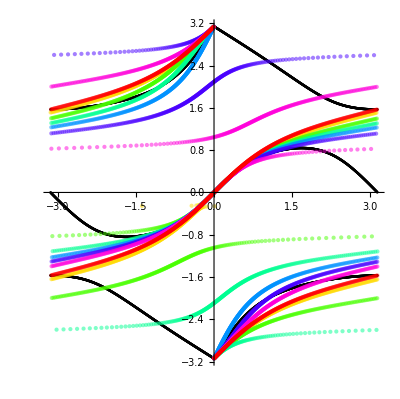

```mathematica
Show[fixed,Table[ListPlot[Arg[Nest[Map[F], input[[i]],1]], PlotRange-> {{-Pi, Pi}, {-Pi, Pi}}, PlotStyle->{ PointSize->Small,Opacity[.5], Hue[i/7]}],{i, 1, 7}],Axes->True, AspectRatio->Full,PlotRange->All]
```

```mathematica
(*compute animation frames *)absmall = Table[Show[{fixed,Table[ListPlot[Arg[Nest[Map[F], input[[i]],n]], PlotRange-> {{-Pi, Pi}, {-Pi, Pi}}, PlotStyle->{ PointSize->Small,Opacity[.5], Hue[i/7]}],{i, 1, 7}]},Axes->True, AspectRatio->Full],{n,1,10}];
```

```mathematica
(* add the input points as the first frame and expost the animation *)PrependTo[absmall, Show[fixed,frame1]];
Export["nevrep.gif", absmall, "AnimationRepetitions"-> ∞, "DisplayDurations"-> .3]
```

nevrep.gif